```mathematica
Clear["Global`*"];
(* All in mkm *)
```

```mathematica
λ=1.55;
n=1;
β=(2π n)/λ;
CalcWindow=50;
N0=127;
ω0=10;
```

```mathematica
ω[z_]:=N[ω0 √(1+((λ z)/(π ω0^2))^2)];
R[z_]:=N[z(1+((π ω0^2)/(λ z))^2)];
q0=N[(π ω0^2)/(I λ)];
zR=Re[I q0];
q[z_]:=Piecewise[{{(-1/R[z]+I λ/(π ω[z]^2))^-1,z<0||z>0}},q0];
Gauss[r_,z_]:=N[Exp[I(β r^2)/2 1/q[z]]];
```

```mathematica
L0=-zR;
StartBeam=Array[Gauss[√(#1^2+#2^2),L0]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
D2Fourier=N[(π/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}]];
FourierOp[h_]:=Exp[I (D2Fourier h)/(2β)];
```

```mathematica
L=2zR;
Nplot=100;
Beam=Parallelize[Table[Abs[InverseFourier[FourierOp[l] Fourier[StartBeam ]][[(N0+1)/2]]]^2,{l,0,L,L/Nplot}]];
```

```mathematica
ListPlot[Arg[(InverseFourier[FourierOp[0] Fourier[StartBeam ]])[[(N0+1)/2]]]];
```

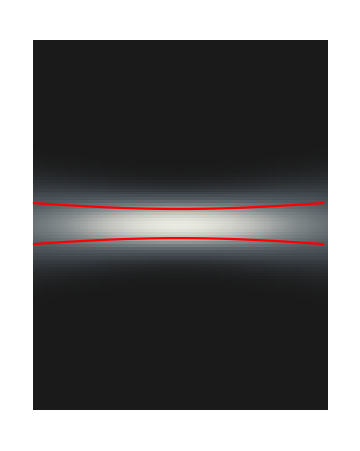

```mathematica
Show[
ArrayPlot[Transpose[Beam],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
Plot[(N0+1)/2+1/2 ω[L0+z×L/Nplot],{z,0,Nplot},ColorFunction->Function[{x,y},Red]],
Plot[(N0+1)/2-1/2 ω[L0+z×L/Nplot],{z,0,Nplot},ColorFunction->Function[{x,y},Red]]
]
```

```mathematica
FinalBeam=InverseFourier[FourierOp[L] Fourier[StartBeam ]];
```

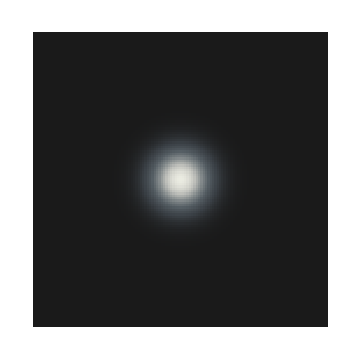
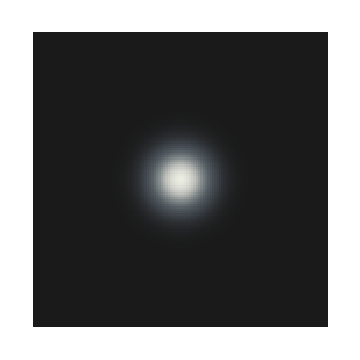
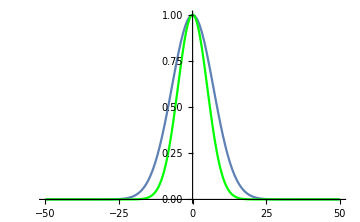
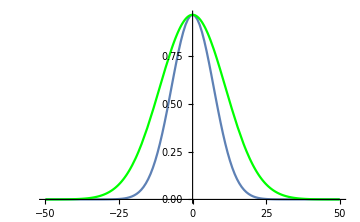
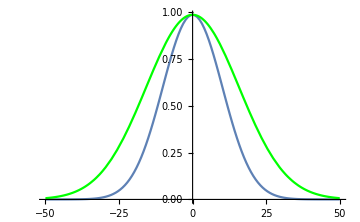

```mathematica
{
ArrayPlot[Abs[StartBeam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],ArrayPlot[Abs[FinalBeam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
Show[
ListPlot[Abs[StartBeam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ImageSize->Medium],
Plot[Abs[Gauss[r,0]]^2,{r,-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Green],ImageSize->Medium]
],
Show[
ListPlot[Abs[FinalBeam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ImageSize->Medium],
Plot[Abs[Gauss[r,L]]^2×Abs[FinalBeam[[(N0+1)/2,(N0+1)/2]]]^2/Abs[Gauss[0,L]]^2,{r,-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Green],ImageSize->Medium]
],
Show[
ListPlot[Abs[FinalBeam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ImageSize->Medium],
Plot[Abs[Gauss[r,L]]×Abs[FinalBeam[[(N0+1)/2,(N0+1)/2]]]/Abs[Gauss[0,L]],{r,-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Green],ImageSize->Medium]
]
}
```

```mathematica
ListPlot3D[Beam,PlotRange->All,ImageSize->Medium,DataRange->{{-CalcWindow,CalcWindow},{0,L}},Mesh->Automatic]
```

-Graphics3D-